```mathematica
Quit
```

## Load Tools

### Load utilities

```mathematica
Module[{nb},
nb=NotebookOpen[FileNameJoin[{NotebookDirectory[],"Utilities.nb"}],CellContext->"Global`",Visible->False];
NotebookEvaluate[nb,InsertResults->False];
NotebookClose[nb]
]
```

FeynCalc 9.3.0 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynHelpers 1.2.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

FeynArts 3.11 (2 Sep 2019) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
model=FileNameJoin[{"KineticMixingDM","KineticMixingDM"}];
genericModel={"Lorentz",model};
```

```mathematica
SetOptions[GenerateDiagrams,Model->model,GenericModel->genericModel];
SetOptions[ComputeAmplitude,Model->model,GenericModel->genericModel,FinalSubstitutions->M$FACouplings,DropSumOver->True];
SetOptions[ComputeAmplitudeSquared,Model->model,GenericModel->genericModel,FinalSubstitutions->M$FACouplings,DropSumOver->True];
SetOptions[ComputeCrossSection22,Model->model,GenericModel->genericModel,FinalSubstitutions->M$FACouplings,DropSumOver->True];
SetOptions[ComputeWidth,Model->model,GenericModel->genericModel,FinalSubstitutions->M$FACouplings,DropSumOver->True];
```

### Particles Names

```mathematica
ElectronNeutrino=F[1,{1}];
MuonNeutrino=F[1,{2}];
TauNeutrino=F[1,{3}];
Electron=F[2,{1}];
Muon=F[2,{2}];
Tau=F[2,{3}];
UpQuark=F[3,{1}];
CharmQuark=F[3,{2}];
TopQuark=F[3,{3}];
DownQuark=F[4,{1}];
StrangeQuark=F[4,{2}];
BottomQuark=F[4,{3}];
DM=F[5];
Higgs=S[1];
VectorMediator=V[5];
Photon=V[1];
ZBoson=V[2];
WBoson=V[3];
```

### JuliaForm

```mathematica
Cot
```

```mathematica
JuliaFormConstantReplacements={
"Pi"->"pi"
};

JuliaFormFuncReplacements={
"**"->"^",
"Sqrt"->"sqrt",
"Log"->"log",
(* Regular Trig *)
"Sin"->"sin",
"Cos"->"cos",
"Tan"->"tan",
"Sec"->"sec",
"Csc"->"csc",
"Cot"->"cot",
(* Inverse Trig *)
"ArcSin"->"asin",
"ArcCos"->"acos",
"ArcTan"->"atan",
"ArcSec"->"asec",
"ArcCsc"->"acsc",
"ArcCot"->"acot",
(* Hyperbolic Trig *)
"Sinh"->"sinh",
"Cosh"->"cosh",
"Tanh"->"tanh",
"Sech"->"sech",
"Csch"->"csch",
"Coth"->"coth",
(* Inverse Hyperbolic Trig *)
"ArcSinh"->"asinh",
"ArcCosh"->"acosh",
"ArcTanh"->"atanh",
"ArcSech"->"asech",
"ArcCsch"->"acsch",
"ArcCoth"->"acoth",
(* Bessel functions *)
"BesselJ"->"besselj",
"BesselY"->"bessely",
"BesselI"->"besseli",
"BesselK"->"besselk"
};

JuliaFormSMParameterReplacements={
"Mu"->"mu",
"Md"->"md",
"Me"->"ml",
"MH"->"HIGGS_MASS",
"MZ"->"Z_BOSON_MASS",
"MW"->"W_BOSON_MASS",
"cw"->"COS_THETA_WEAK",
"sw"->"SIN_THETA_WEAK",
"alphaEM"->"ALPHA_EM",
"vev"->"HIGGS_VEV"
};

JuliaFormParameterReplacements={
"MDM"->"model.mx",
"MV"->"model.mv",
"gVXX"->"model.gvxx",
"eps"->"model.eps",
"ΓV"->"width_v"
};

JuliaForm[expr_]:=Module[{},
StringReplace[ToString[expr,FortranForm],
Join[JuliaFormFuncReplacements,JuliaFormSMParameterReplacements,JuliaFormParameterReplacements,JuliaFormConstantReplacements]]]
```

## Widths

```mathematica
WidthVtoXX=ComputeWidth[{VectorMediator}->{DM,-DM},List->False]//FullSimplify;
JuliaForm[WidthVtoXX/.Ncol->1]
```

(model.gvxx^2*sqrt(-4*model.mx^2 + model.mv^2)*(2*model.mx^2 + model.mv^2))/(12.*model.mv^2*pi)

```mathematica
WidthVtoνν=ComputeWidth[{VectorMediator}->{ElectronNeutrino,-ElectronNeutrino},List->False]/.{FCGV["MU"]->Mu}//FullSimplify[#,Assumptions->{MV>0}]&;
JuliaForm[WidthVtoνν/.Ncol->1]
```

(ALPHA_EM*model.eps^2*model.mv)/(24.*COS_THETA_WEAK^2)

```mathematica
WidthVtoLL=ComputeWidth[{VectorMediator}->{Electron,-Electron},List->False]/.{FCGV["ME"]->Me}//FullSimplify;
JuliaForm[WidthVtoLL/.Ncol->1]
```

(ALPHA_EM*model.eps^2*sqrt(-4*ml^2 + model.mv^2)*(7*ml^2 + 5*model.mv^2))/(24.*COS_THETA_WEAK^2*model.mv^2)

```mathematica
WidthVtoUU=ComputeWidth[{VectorMediator}->{UpQuark,-UpQuark},List->False]/.{FCGV["MU"]->Mu}//FullSimplify;
JuliaForm[WidthVtoUU/.Ncol->3]
```

(ALPHA_EM*model.eps^2*sqrt(-4*mu^2 + model.mv^2)*(7*mu^2 + 17*model.mv^2))/(72.*COS_THETA_WEAK^2*model.mv^2)

```mathematica
WidthVtoDD=ComputeWidth[{VectorMediator}->{DownQuark,-DownQuark},List->False]/.{FCGV["MD"]->Md}//FullSimplify;
JuliaForm[WidthVtoDD/.Ncol->3]
```

(ALPHA_EM*model.eps^2*sqrt(-4*md^2 + model.mv^2)*(-17*md^2 + 5*model.mv^2))/(72.*COS_THETA_WEAK^2*model.mv^2)

```mathematica
WidthVtoHZ=ComputeWidth[{VectorMediator}->{Higgs,ZBoson},List->False]/.{FCGV["MZ"]->MZ,FCGV["MH"]->MH}//FullSimplify;
JuliaForm[WidthVtoHZ]
```

(ALPHA_EM^2*model.eps^2*sqrt(-HIGGS_MASS^2 + (HIGGS_MASS^2 + model.mv^2 - Z_BOSON_MASS^2)^2/(4.*model.mv^2))*(2*model.mv^2*Z_BOSON_MASS^2 + (-HIGGS_MASS^2 + model.mv^2 + Z_BOSON_MASS^2)^2/4.)*pi*vev^2)/(6.*COS_THETA_WEAK^4*model.mv^4*Z_BOSON_MASS^2*SIN_THETA_WEAK^2)

## Annihilation Cross Sections

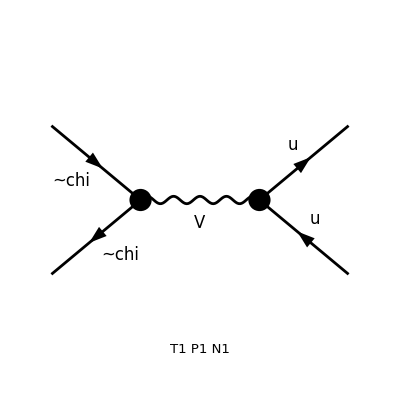

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

(ALPHA_EM*model.eps^2*model.gvxx^2*(2*model.mx^2 + Q^2)*sqrt(-4*mu^2 + Q^2)*(7*mu^2 + 17*Q^2))/(72.*COS_THETA_WEAK^2*Q^2*sqrt(-4*model.mx^2 + Q^2)*((model.mv^2 - Q^2)^2 + model.mv^2*width_v^2))

```mathematica
CrossSectionXXtoUU=First[ComputeCrossSection22[{DM,-DM}->{UpQuark,-UpQuark},Q,Paint->True,ColumnsXRows->{2,1}]/.{yu[1,1]->√2 Mu/vev,FCGV["MU"]->Mu,SMP["m_u"]->Mu}//FullSimplify[#,Assumptions->{Mu>0,vev>0}]&];
JuliaForm[CrossSectionXXtoUU/.Ncol->3]
```

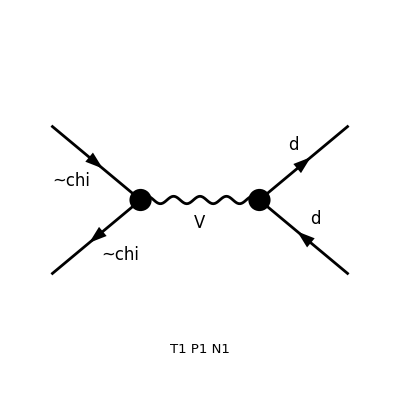

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

(ALPHA_EM*model.eps^2*model.gvxx^2*sqrt(-4*md^2 + Q^2)*(2*model.mx^2 + Q^2)*(-17*md^2 + 5*Q^2))/(72.*COS_THETA_WEAK^2*Q^2*sqrt(-4*model.mx^2 + Q^2)*((model.mv^2 - Q^2)^2 + model.mv^2*width_v^2))

```mathematica
CrossSectionXXtoDD=First[ComputeCrossSection22[{DM,-DM}->{DownQuark,-DownQuark},Q,Paint->True,ColumnsXRows->{2,1}]/.{yu[1,1]->√2 Mu/vev,FCGV["MD"]->Md,SMP["m_u"]->Mu}//FullSimplify[#,Assumptions->{Mu>0,vev>0}]&];
JuliaForm[CrossSectionXXtoDD/.Ncol->3]
```

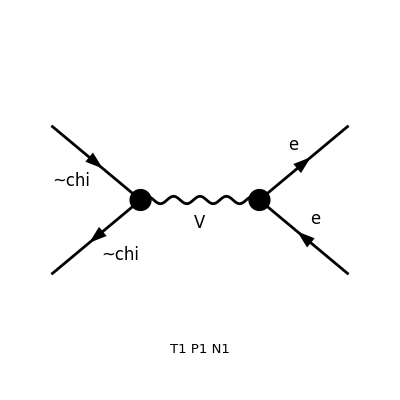

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

(alphaEM eps^2 gVXX^2 (2 MDM^2+Q^2) √(Q^2-4 Me^2) (7 Me^2+5 Q^2))/(24 cw^2 Q^2 √(Q^2-4 MDM^2) (ΓV^2 MV^2+(MV^2-Q^2)^2))

(ALPHA_EM*model.eps^2*model.gvxx^2*(2*model.mx^2 + Q^2)*sqrt(-4*ml^2 + Q^2)*(7*ml^2 + 5*Q^2))/(24.*COS_THETA_WEAK^2*Q^2*sqrt(-4*model.mx^2 + Q^2)*((model.mv^2 - Q^2)^2 + model.mv^2*width_v^2))

```mathematica
CrossSectionXXtoLL=First[ComputeCrossSection22[{DM,-DM}->{Electron,-Electron},Q,Paint->True,ColumnsXRows->{2,1}]/.{yu[1,1]->√2 Mu/vev,FCGV["MD"]->Md,SMP["m_u"]->Mu}//FullSimplify[#,Assumptions->{Mu>0,vev>0}]&]
JuliaForm[CrossSectionXXtoLL]
```

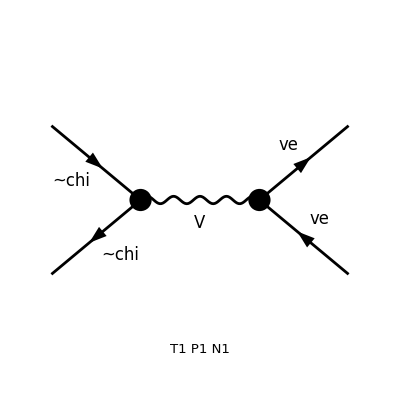

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

(ALPHA_EM*model.eps^2*model.gvxx^2*sqrt(Q^2)*(2*model.mx^2 + Q^2))/(24.*COS_THETA_WEAK^2*sqrt(-4*model.mx^2 + Q^2)*((model.mv^2 - Q^2)^2 + model.mv^2*width_v^2))

```mathematica
CrossSectionXXtoνν=First[ComputeCrossSection22[{DM,-DM}->{ElectronNeutrino,-ElectronNeutrino},Q,Paint->True,ColumnsXRows->{2,1}]/.{yu[1,1]->√2 Mu/vev,FCGV["MD"]->Md,SMP["m_u"]->Mu}//FullSimplify[#,Assumptions->{Mu>0,vev>0}]&];
JuliaForm[CrossSectionXXtoνν]
```

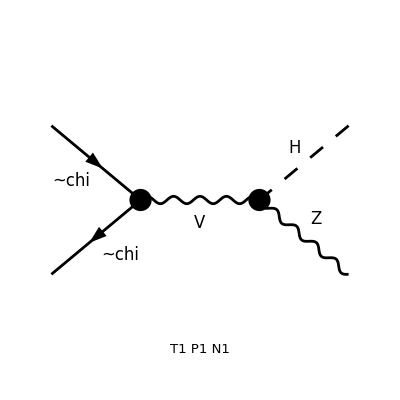

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

(ALPHA_EM^2*model.eps^2*model.gvxx^2*pi*sqrt(((HIGGS_MASS - Z_BOSON_MASS - Q)*(HIGGS_MASS + Z_BOSON_MASS - Q)*(HIGGS_MASS - Z_BOSON_MASS + Q)*(HIGGS_MASS + Z_BOSON_MASS + Q))/(-4*model.mx^2 + Q^2))*(2*model.mx^2 + Q^2)*(HIGGS_MASS^4 + Z_BOSON_MASS^4 + 10*Z_BOSON_MASS^2*Q^2 + Q^4 - 2*HIGGS_MASS^2*(Z_BOSON_MASS^2 + Q^2))*HIGGS_VEV^2)/(48.*COS_THETA_WEAK^4*Z_BOSON_MASS^2*Q^5*SIN_THETA_WEAK^2*((model.mv^2 - Q^2)^2 + model.mv^2*width_v^2))

```mathematica
CrossSectionXXtoHZ=First[ComputeCrossSection22[{DM,-DM}->{Higgs,ZBoson},Q,Paint->True,ColumnsXRows->{2,1}]/.{yu[1,1]->√2 Mu/vev,FCGV["MH"]->MH,FCGV["MZ"]->MZ,SMP["m_u"]->Mu}//FullSimplify[#,Assumptions->{Mu>0,vev>0,Q>MZ+MH>0,Q>2MDM>0,MZ>0,MH>0,MDM>0}]&];
JuliaForm[CrossSectionXXtoHZ]
```

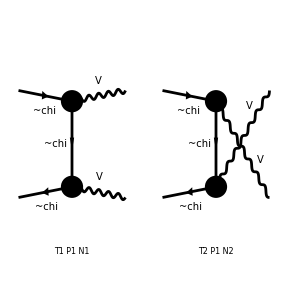

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

{1/(24 (16 π Q^4-64 MDM^2 π Q^2))gVXX^4 (1/(MV^8-4 MDM^2 MV^6+MDM^2 Q^2 MV^4)√(Q^2-4 MDM^2) √(Q^2-4 MV^2) (-48 MV^8+20 (2 MDM^2+Q^2) MV^6+(-256 MDM^4-102 Q^2 MDM^2+Q^4) MV^4+16 MDM^2 Q^2 (2 MDM^2+Q^2) MV^2+MDM^2 Q^4 (2 MDM^2+Q^2))+24 (Q^2+2 (MDM-MV) (MDM+MV)) (log(2 MV^2-Q^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2))-log(2 MV^2-Q^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2)))),(gVXX^4 (-48 (MDM^2 Q^4+(2 MDM^4-6 MV^2 MDM^2+MV^4) Q^2-2 (MV^6-5 MDM^2 MV^4+4 MDM^4 MV^2)) log(-2 MV^2+Q^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+48 (MDM^2 Q^4+(2 MDM^4-6 MV^2 MDM^2+MV^4) Q^2-2 (MV^6-5 MDM^2 MV^4+4 MDM^4 MV^2)) log(-2 MV^2+Q^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+2 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) (MDM^2 Q^6+(2 MDM^4+16 MV^2 MDM^2+MV^4) Q^4+2 (10 MV^6-51 MDM^2 MV^4+16 MDM^4 MV^2) Q^2-8 (6 MV^8-5 MDM^2 MV^6+32 MDM^4 MV^4))))/(48 MV^4 (MV^4-4 MDM^2 MV^2+MDM^2 Q^2) (16 π Q^4-64 MDM^2 π Q^2)),(gVXX^4 (48 ((MDM^2+2 MV^2) Q^2-2 MDM^2 (2 MDM^2+MV^2)) log(2 MV^2-Q^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+48 (2 MDM^2 (2 MDM^2+MV^2)-(MDM^2+2 MV^2) Q^2) log(-2 MV^2+Q^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+48 (2 MDM^2 (2 MDM^2+MV^2)-(MDM^2+2 MV^2) Q^2) log(2 MV^2-Q^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+48 ((MDM^2+2 MV^2) Q^2-2 MDM^2 (2 MDM^2+MV^2)) log(-2 MV^2+Q^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4-(Q^2-2 MV^2) (4 MV^6-42 Q^2 MV^4+8 MDM^2 (5 √(Q^2-4 MDM^2) √(Q^2-4 MV^2)-12 MV^2) MV^2+20 Q^2 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) MV^2+Q^6+Q^4 (18 MV^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2))+2 MDM^2 Q^2 (24 MV^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2)))+(Q^2-2 MV^2) (4 MV^6+Q^6+Q^4 (18 MV^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2))-8 MDM^2 (12 MV^4+5 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) MV^2)-2 Q^2 (21 MV^4+10 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) MV^2+MDM^2 (√(Q^2-4 MDM^2) √(Q^2-4 MV^2)-24 MV^2)))))/(24 MV^4 (Q^2-2 MV^2) (16 π Q^4-64 MDM^2 π Q^2))}

```mathematica
CrossSectionXXtoVV=ComputeCrossSection22[{DM,-DM}->{VectorMediator,VectorMediator},Q,Paint->True]
```

```mathematica
CrossSectionXXtoVV=Simplify[Total[CrossSectionXXtoVV]]
```

1/(768 π Q^2 (Q^2-4 MDM^2))gVXX^4 (1/(MV^8+MDM^2 (MV^4 Q^2-4 MV^6))2 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) (-48 MV^8+20 Q^2 MV^6+Q^4 MV^4+MDM^4 (-256 MV^4+32 Q^2 MV^2+2 Q^4)+MDM^2 (40 MV^6-102 Q^2 MV^4+16 Q^4 MV^2+Q^6))+48 (2 MDM^2-2 MV^2+Q^2) (log(2 MV^2-Q^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2))-log(2 MV^2-Q^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2)))+1/(MV^4 (Q^2-2 MV^2))2 (48 (-4 MDM^4+(Q^2-2 MV^2) MDM^2+2 MV^2 Q^2) log(2 MV^2-Q^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+48 (2 MDM^2 (2 MDM^2+MV^2)-(MDM^2+2 MV^2) Q^2) log(-2 MV^2+Q^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+48 (2 MDM^2 (2 MDM^2+MV^2)-(MDM^2+2 MV^2) Q^2) log(2 MV^2-Q^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+48 (-4 MDM^4+(Q^2-2 MV^2) MDM^2+2 MV^2 Q^2) log(-2 MV^2+Q^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+(Q^2-2 MV^2) (4 MV^6+Q^6+Q^4 (18 MV^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2))-8 MDM^2 (12 MV^4+5 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) MV^2)-2 Q^2 (21 MV^4+10 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) MV^2+MDM^2 (√(Q^2-4 MDM^2) √(Q^2-4 MV^2)-24 MV^2)))-(Q^2-2 MV^2) (4 MV^6-42 Q^2 MV^4+2 (9 Q^4+10 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) Q^2) MV^2+Q^6+2 MDM^2 (-48 MV^4+4 (6 Q^2+5 √(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^2+Q^2 √(Q^2-4 MDM^2) √(Q^2-4 MV^2))+Q^4 √(Q^2-4 MDM^2) √(Q^2-4 MV^2)))+1/(MV^4 (MV^4+MDM^2 (Q^2-4 MV^2)))(-48 (-2 MV^6+Q^2 MV^4+MDM^4 (2 Q^2-8 MV^2)+MDM^2 (10 MV^4-6 Q^2 MV^2+Q^4)) log(-2 MV^2+Q^2-√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+48 (-2 MV^6+Q^2 MV^4+MDM^4 (2 Q^2-8 MV^2)+MDM^2 (10 MV^4-6 Q^2 MV^2+Q^4)) log(-2 MV^2+Q^2+√(Q^2-4 MDM^2) √(Q^2-4 MV^2)) MV^4+2 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) (-48 MV^8+20 Q^2 MV^6+Q^4 MV^4+MDM^4 (-256 MV^4+32 Q^2 MV^2+2 Q^4)+MDM^2 (40 MV^6-102 Q^2 MV^4+16 Q^4 MV^2+Q^6))))

```mathematica
CrossSectionXXtoVV=Simplify[ReplaceAll[CrossSectionXXtoVV,{
c_.Log[a_]+c_.Log[b_]:>c Log[a*b],
c_.Log[a_]-c_.Log[b_]:>c Log[a/b]
}]];
CrossSectionXXtoVV=FullSimplify[ReplaceAll[CrossSectionXXtoVV,{
c_.Log[a_]+c_.Log[b_]:>c Log[a*b],
c_.Log[a_]-c_.Log[b_]:>c Log[a/b]
}]];
CrossSectionXXtoVV=Simplify[ReplaceAll[CrossSectionXXtoVV,{
c_.Log[a_]+c_.Log[b_]:>c Log[a*b],
c_.Log[a_]-c_.Log[b_]:>c Log[a/b]
}]]
```

1/(16 π Q^2 (Q^2-4 MDM^2))gVXX^4 (-(2 MDM^2-2 MV^2+Q^2) log(-√(Q^2-4 MDM^2) √(Q^2-4 MV^2)-2 MV^2+Q^2)+(2 MDM^2-2 MV^2+Q^2) log(-((√(Q^2-4 MDM^2) √(Q^2-4 MV^2)-2 MV^2+Q^2)^2)/(√(Q^2-4 MDM^2) √(Q^2-4 MV^2)+2 MV^2-Q^2))+(2 (-4 MDM^4+MDM^2 (Q^2-2 MV^2)+2 MV^2 Q^2) log(-(√(Q^2-4 MDM^2) √(Q^2-4 MV^2)+2 MV^2-Q^2)^2))/(2 MV^2-Q^2)+(2 (-4 MDM^4+MDM^2 (Q^2-2 MV^2)+2 MV^2 Q^2) log(-(√(Q^2-4 MDM^2) √(Q^2-4 MV^2)-2 MV^2+Q^2)^2))/(Q^2-2 MV^2)-(2 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) (4 MDM^4+MDM^2 Q^2+2 MV^4))/(MDM^2 (Q^2-4 MV^2)+MV^4))

```mathematica
CrossSectionXXtoVV//StandardForm
```

1/(16 π Q^2 (-4 MDM^2+Q^2))gVXX^4 (-(2 √(-4 MDM^2+Q^2) √(-4 MV^2+Q^2) (4 MDM^4+2 MV^4+MDM^2 Q^2))/(MV^4+MDM^2 (-4 MV^2+Q^2))+(2 (-4 MDM^4+2 MV^2 Q^2+MDM^2 (-2 MV^2+Q^2)) Log[-(2 MV^2-Q^2+√(-4 MDM^2+Q^2) √(-4 MV^2+Q^2))^2])/(2 MV^2-Q^2)+(2 (-4 MDM^4+2 MV^2 Q^2+MDM^2 (-2 MV^2+Q^2)) Log[-(-2 MV^2+Q^2+√(-4 MDM^2+Q^2) √(-4 MV^2+Q^2))^2])/(-2 MV^2+Q^2)+(2 MDM^2-2 MV^2+Q^2) Log[((-2 MV^2+Q^2+√(-4 MDM^2+Q^2) √(-4 MV^2+Q^2))^2)/((2 MV^2-Q^2+√(-4 MDM^2+Q^2) √(-4 MV^2+Q^2))^2)])

```mathematica
CrossSectionXXtoVV=Simplify[1/(16 π Q^2 (-4 MDM^2+Q^2))gVXX^4 (-(2 √(-4 MDM^2+Q^2) √(-4 MV^2+Q^2) (4 MDM^4+2 MV^4+MDM^2 Q^2))/(MV^4+MDM^2 (-4 MV^2+Q^2))+(2 (-4 MDM^4+2 MV^2 Q^2+MDM^2 (-2 MV^2+Q^2)) Log[(-(-2 MV^2+Q^2+√(-4 MDM^2+Q^2) √(-4 MV^2+Q^2))^2)/(-(2 MV^2-Q^2+√(-4 MDM^2+Q^2) √(-4 MV^2+Q^2))^2)])/(-2 MV^2+Q^2)+(2 MDM^2-2 MV^2+Q^2) Log[((-2 MV^2+Q^2+√(-4 MDM^2+Q^2) √(-4 MV^2+Q^2))^2)/((2 MV^2-Q^2+√(-4 MDM^2+Q^2) √(-4 MV^2+Q^2))^2)])]
```

1/(16 π Q^2 (Q^2-4 MDM^2))gVXX^4 ((2 MDM^2-2 MV^2+Q^2) log(((√(Q^2-4 MDM^2) √(Q^2-4 MV^2)-2 MV^2+Q^2)^2)/((√(Q^2-4 MDM^2) √(Q^2-4 MV^2)+2 MV^2-Q^2)^2))+(2 (-4 MDM^4+MDM^2 (Q^2-2 MV^2)+2 MV^2 Q^2) log(((√(Q^2-4 MDM^2) √(Q^2-4 MV^2)-2 MV^2+Q^2)^2)/((√(Q^2-4 MDM^2) √(Q^2-4 MV^2)+2 MV^2-Q^2)^2)))/(Q^2-2 MV^2)-(2 √(Q^2-4 MDM^2) √(Q^2-4 MV^2) (4 MDM^4+MDM^2 Q^2+2 MV^4))/(MDM^2 (Q^2-4 MV^2)+MV^4))

```mathematica
JuliaForm[CrossSectionXXtoVV]
```

(model.gvxx^4*((-2*sqrt(-4*model.mx^2 + Q^2)*sqrt(-4*model.mv^2 + Q^2)*(4*model.mx^4 + 2*model.mv^4 + model.mx^2*Q^2))/(model.mv^4 + model.mx^2*(-4*model.mv^2 + Q^2)) + (2*model.mx^2 - 2*model.mv^2 + Q^2)*log((-2*model.mv^2 + Q^2 + sqrt(-4*model.mx^2 + Q^2)*sqrt(-4*model.mv^2 + Q^2))^2/(2*model.mv^2 - Q^2 + sqrt(-4*model.mx^2 + Q^2)*sqrt(-4*model.mv^2 + Q^2))^2) + (2*(-4*model.mx^4 + 2*model.mv^2*Q^2 + model.mx^2*(-2*model.mv^2 + Q^2))*log((-2*model.mv^2 + Q^2 + sqrt(-4*model.mx^2 + Q^2)*sqrt(-4*model.mv^2 + Q^2))^2/(2*model.mv^2 - Q^2 + sqrt(-4*model.mx^2 + Q^2)*sqrt(-4*model.mv^2 + Q^2))^2))/(-2*model.mv^2 + Q^2)))/(16.*pi*Q^2*(-4*model.mx^2 + Q^2))

```mathematica
res==√s=mv=z*mx
zres=mv/mx
```

```mathematica
thr==√s=2mv=z*mx
zthr=2mv/mx
```

```mathematica
2<z<Inf
```

```mathematica
thres only if:
2<2mv/mx
mx<mv
res only if:
mx<2mx<mv
```

```mathematica
mv<mx
```

```mathematica
Series[BesselK[n,x]Exp[x],{x,Infinity,1}]
```

√(π/2) √(1/x)+O((1/x)^(3/2))

```mathematica
Limit[BesselK[1,x]Exp[x],x->∞]
```

0

```mathematica
ReplaceAll[D[BesselK[n,x]Exp[x],x]//Expand,Exp[x_]BesselK[n_,x_]:>Ke[n,x]]
```

-1/2 Ke(n-1,x)+Ke(n,x)-1/2 Ke(n+1,x)

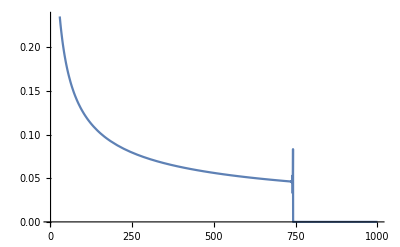

```mathematica
Plot[BesselK[1,x]Exp[x],{x,1,1000}]
```